## §7. Ряды Фурье. Интеграл Фурье.

### 7.1. Разложение функций в тригонометрические ряды Фурье.

Тригонометрическая система функций

1,cos x, sin x, cos 2x, sin 2x,..., cos n x,sin n x,...

является ортогональной на отрезке [-π,π] (как, впрочем, и на всяком отрезке длины 2π), т.е. интеграл по этому отрезку от произведения любых двух различных функций этой системы равен нулю.

Если f(x) ∈L(-π,π) (т.е. ∫_-π^π |f(x)|ⅆx<+∞), то существуют числа

a_n=1/π∫_-π^π f(x)cos(n x)ⅆx    n=0,1,2,...

b_n=1/π∫_-π^π f(x)sin(n x)ⅆx, n=1,2,...

называемые коэффициентами Фурье функции f(x).

Ряд

S(x)=a_0/2+∑_(n=1)^∞ (a_n cos(n x)+b_n sin(n x))

называется рядом Фурье функции f(x).

Члены ряда (1) можно записать в виде гармоник

a_n cos(n x)+b_n sin(n x)=A_n cos(n x-ϕ_n)

с амплитудой A_n=√(a_n^2+b_n^2) , частотой ω_n=n и фазой ϕ_n=arctg b_n/a_n.

Для функции f(x) такой, что f^2(x)∈L(-π,π), справедливо равенство Парсеваля

1/π∫_-π^π f^2(x)ⅆx=a_0^2/2+∑_(n=1)^∞ (a_n^2+b_n^2)

Если же f(x) ∈L(-l,l) , то коэффициенты Фурье записываются в виде:

a_0=1/l∫_-l^l f(x)ⅆx

a_n=1/l∫_-l^l f(x)cos(π/l n x)ⅆx

b_n=1/l∫_-l^l f(x)sin(π/l n x)ⅆx

а ряд Фурье - в виде

S(x)=a_0/2+∑_(n=1)^∞ (a_n cos(π/l n x)+b_n sin(π/l n x))

Суммы рядов (1), (5),(6) имеют периоды соответственно 2π, 2l,2l

Функция f(x) называется кусочно гладкой на отрезке [a;b], если сама функция f(x) и ее производная f’(x) имеют на [a;b] конечное число точек разрыва 1-ого рода.

Т е о р е м а. Если периодическая функция f(x) с периодом 2l кусочно гладка на отрезке [-l;l], то ряд Фурье (5) сходится к значению f(x) в каждой ее точке непрерывности и к значению  (f(x+0)+f(x-0))/2 в точке разрыва, т.е.

1/2(f(x+0)+f(x-0))=a_0/2+∑_(n=1)^∞ (a_n cos(π/l n x)+b_n sin(π/l n x))

Если, дополнительно, f(x) непрерывна на всей оси, то ряд (6) сходится к f(x) равномерно.

Если на полуоткрытом интервали длины 2l, т.е. на интервале вида [a,a+2l) или (a,a+2l], определена какая-нибудь функция, то она может быть (единственным способом) продолжена на всю числовую прямую так, что получится функция с периодом 2l.

Отсюда следует, что если f(x) имеет на [-l,l] не более конечного числа точек разрыва и абсолютно интегрируема на этом сегменте, то она разложима в ряд фурье (5).

##### Пример №12.480

Разложить периодическую функцию с периодом 2l функцию в ряд Фурье, построить график.

f(x)=Piecewise[{{1, при 0<x<π}, {0, при -π<x<0}}]

Запишем исходную кусочно-заданную функцию и построим ее график:

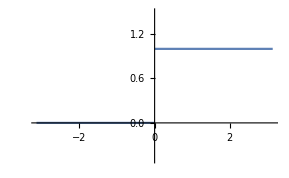

```mathematica
f[x_]:=Piecewise[{{1,0<x<Pi},{0,-Pi<x<0}}]
Plot[f[x],{x,-Pi,Pi},PlotRange->{-0.5,1.5}]
```

Запишем выражения для коэффициентов Фурье по формулам (2), (3), (4)

Так как функция обращается в ноль при x<0, интегрирование ведем от 0 до π

Коэффициент a_0 вычисляется следующим образом:

```mathematica
a0=1/π Integrate[f[x],{x,0,Pi}]
```

1

Коэффициент a_n

```mathematica
an=1/π Integrate[f[x]Cos[n x],{x,0,Pi}]
```

Sin[n π]/(n π)

При любых n, a_n=0, но a_0=1

Теперь коэффициент b_n

```mathematica
bn=1/π Integrate[f[x]Sin[n x],{x,0,Pi}]
```

(1-Cos[n π])/(n π)

Получили, что коэффициент b_n:

b_n=Piecewise[{{2/((2k+1) π), при n=2k+1}, {0, при n=2k}}]

Запишем ряд Фурье:

f(x)=1/2+∑_(k=0)^∞ (2sin((2k+1)x))/((2k+1)π)

```mathematica
fu[x_,n_]:=1/2+2/π Sum[Sin[(2k+1)x]/(2k+1),{k,0,n}]
```

```mathematica
fu[x,4]//Expand
```

1/2+(2 Sin[x])/π+(2 Sin[3 x])/(3 π)+(2 Sin[5 x])/(5 π)+(2 Sin[7 x])/(7 π)+(2 Sin[9 x])/(9 π)

Изобразим график исходной функции и ряда Фурье до 4ого и до 10ого члена.

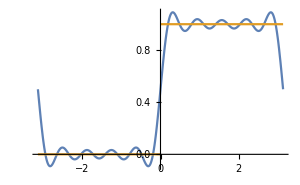
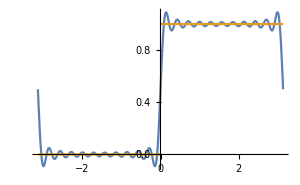

```mathematica
Row[{Plot[{fu[x,4],f[x]},{x,-Pi,Pi},ImageSize->300],Plot[{Fu[x,10],f[x]},{x,-Pi,Pi},ImageSize->300] }]
```

Из графиков видно, что чем больше максимальный парядок разложения, тем сильнее совпадают функция и ее ряд.

В данной задаче было показано, как, на основе определений коэффициентов, разложить функцию в ряд Фурье.

##### Пример №12.487

Разложить периодическую функцию с периодом 2l функцию в ряд Фурье, построить график.

f(x)=2x ,       0<x<1, 2l=1

Определим заданную функцию, и построим ее график:

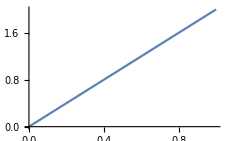

```mathematica
f[x_]:=2x
l=1/2;
Plot[f[x],{x,0,1}]
```

Теперь запишем функции для коэффициентов Фурье по формулам (3), (4), (5):

Так как в формуле (4), при n=0, косинус обращается в единицу, то записывать выражение для коэффициента a_0 смысла нет.

```mathematica
a[n_]:=Integrate[1/l f[x]Cos[Pi n x/l],{x,0,1}];
b[n_]:=Integrate[1/l f[x] Sin[Pi n x/l],{x,0,1}];
```

Теперь запишем функцию тригонометрического ряда Фурье:

```mathematica
fu[x_,k_]:=a[0]/2+Sum[a[n]Cos[Pi/l n x]+b[n]Sin[Pi/l n x],{n,1,k}]
```

Выведем выражение для ряда до 5ого члена и построим его график:

1-(2 Sin[2 π x])/π-Sin[4 π x]/π-(2 Sin[6 π x])/(3 π)-Sin[8 π x]/(2 π)-(2 Sin[10 π x])/(5 π)

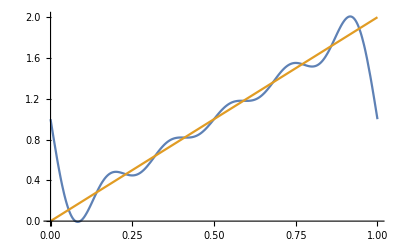

```mathematica
fu[x,5]
Plot[{Evaluate@fu[x,5],f[x]},{x,0,1}]
```

Чтобы проверить себя найдем сумму бесконечного ряда:

```mathematica
fu[x,Infinity]
```

1+(ⅈ (-Log[1-ⅇ^(2 ⅈ π x)]+Log[ⅇ^(-2 ⅈ π x) (-1+ⅇ^(2 ⅈ π x))]))/π

И построим теперь график полученной функции:

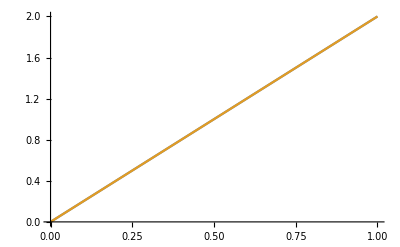

```mathematica
Plot[{f[x],Evaluate@fu[x,Infinity]},{x,0,1}]
```

Графики функций совпали, следовательно, как и предполагалось, ряд сходится к функции.

### 7.2. Особенности разложения в ряд Фурье четных и нечетных функций.

Если функцию обладает какой-либо симметрией, то техника разложения в ряд Фурье упрощается.

В случае, если f(x) - четная функция с периодом 2l, то все коэффициенты Фурье b_n равны 0 и, следовательно, в ряде Фурье нет членов с синусами. Тогда получим ряд:

S(x)=a_0/2+∑_(n=1)^∞ a_n cos(π/l n x)

где

a_0=2/l∫_0^l f(x)ⅆx

a_n=2/l∫_0^l f(x)cos(π/l n x)ⅆx

Аналогично в случае, если f(x) - нечетная функция, то все коэффициенты Фурье a_n равны 0 и, следовательно, в ряде Фурье нет членов с косинусами. Тогда получим ряд:

S(x)=∑_(n=1)^∞ b_n sin(π/l n x)

где

b_n=2/l∫_0^l f(x)sin(π/l n x)ⅆx

##### Пример №12.482

Разложить в ряд Фурье функцию:

f(x)=|x|,  -1<x<1, l=1

Запишем и построим график заданной функции:

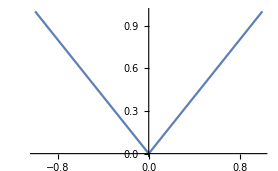

```mathematica
f[x_]:=Abs[x]
Plot[f[x],{x,-1,1}]
```

Так как функция четная, то в разложении будут отсутствовать члены с синусами. Тогда запишем выражение для коэффициента a_n:

```mathematica
a[n_]:=Integrate[2 f[x] Cos[Pi n x],{x,0,1}]
```

Запишем функцию ряда:

```mathematica
fu[x_,k_]:=a[0]/2+Sum[a[n]Cos[Pi n x],{n,1,k}]
```

Выведем полученный ряд до 6ого члена и построим его функцию:

1/2-(4 Cos[π x])/π^2-(4 Cos[3 π x])/(9 π^2)-(4 Cos[5 π x])/(25 π^2)

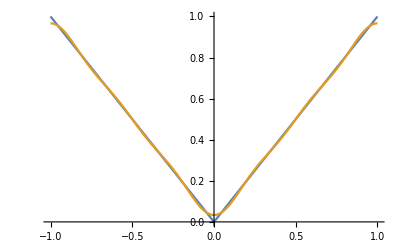

```mathematica
fu[x,6]
Plot[{f[x],Evaluate@fu[x,6]},{x,-1,1}]
```

Из графика заключаем, что ряд сходится к функции.

##### Пример №12.493

Доопределяя необходимым образом заданную в промежутке функцию до переодической, получить для нее: а) ряд Фурье по косинусам б) ряд Фурье по синусам.

f(x)=e^x, 0<x<ln 2

Для того чтобы получить ряд Фурье по косинусам, необходимо чтобы функция была чётной. Функция e^(|x|) подходит под данное требование. Запишем и изобразим эту функцию:

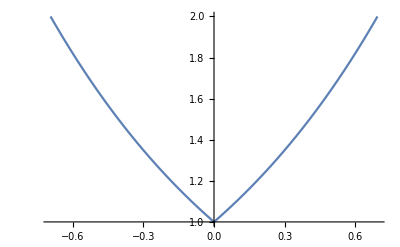

```mathematica
f[x_]:=Exp[Abs[x]]
Plot[f[x],{x,-Log[2],Log[2]}]
```

Теперь получим выражение для коэффициента Фурье и запишем ряд:

```mathematica
a[n_]:=Integrate[2/Log[2] f[x]Cos[Pi/Log[2] n x],{x,0,Log[2]}]
fu[x_,k_]:=a[0]/2+Sum[a[n]Cos[Pi/Log[2] n x],{n,1,k}]
```

Изобразим полученный ряд:

1/Log[2]-(6 Cos[(π x)/Log[2]] Log[2])/(π^2+Log[2]^2)-(6 Cos[(3 π x)/Log[2]] Log[2])/(9 π^2+Log[2]^2)-(6 Cos[(5 π x)/Log[2]] Log[2])/(25 π^2+Log[2]^2)+(Cos[(2 π x)/Log[2]] Log[4])/(4 π^2+Log[2]^2)+(Cos[(4 π x)/Log[2]] Log[4])/(16 π^2+Log[2]^2)

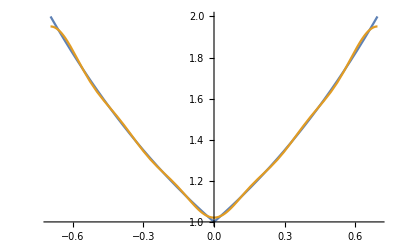

```mathematica
fu[x,5]
Plot[{f[x],Evaluate@fu[x,5]},{x,-Log[2],Log[2]}]
```

Теперь для того чтобы получить разложение Фурье по синусам, доопределим исходную функцию до нечетной следующим образом:

f(x)=Piecewise[{{e^x, 0<x<ln 2}, {-e^-x, -ln 2<x<0}}]

Запишем и построим полученную функцию:

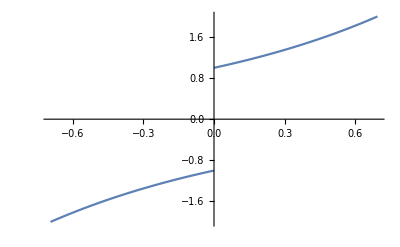

```mathematica
f[x_]:=Piecewise[{{Exp[x],Log[2]>x>0},{-Exp[-x],-Log[2]<x<0}}]
Plot[f[x],{x,-Log[2],Log[2]}]
```

Запишем выражения для коэффициента b_n и ряда:

```mathematica
b[n_]:=Integrate[2/Log[2] f[x]Sin[Pi/Log[2] n x],{x,0,Log[2]}]
fu[x_,k_]:=Sum[b[n]Sin[Pi/Log[2] n x],{n,1,k}]
```

Получим разложение функции до 6ого члена и построим график:

(6 π Sin[(π x)/Log[2]])/(π^2+Log[2]^2)-(4 π Sin[(2 π x)/Log[2]])/(4 π^2+Log[2]^2)+(18 π Sin[(3 π x)/Log[2]])/(9 π^2+Log[2]^2)-(8 π Sin[(4 π x)/Log[2]])/(16 π^2+Log[2]^2)+(30 π Sin[(5 π x)/Log[2]])/(25 π^2+Log[2]^2)-(12 π Sin[(6 π x)/Log[2]])/(36 π^2+Log[2]^2)

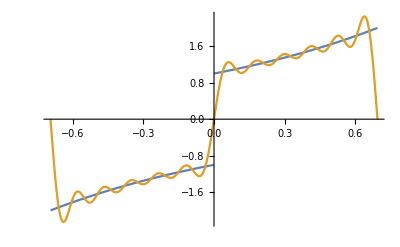

```mathematica
fu[x,6]
Plot[{f[x],Evaluate@fu[x,12]},{x,-Log[2],Log[2]}]
```

В точке разрыва, значение ряда S(0) будет равно:

S(0)=(f(+0)+f(-0))/2

##### Программный модуль

Анализируя последовательность действий в общем случае, напишем простую обучающую программу, которая будет раскладывать функцию в ряд Фурье на заданном интервале [h;g] с полупериодом l=(g-h)/2:

```mathematica
fourier[x_,func_,h_,g_,k_]:=Module[{a,b,l},
l=(g-h)/2;
a[n_]:=Integrate[1/l func Cos[Pi n x/l],{x,h,g}];
b[n_]:=Integrate[1/l func  Sin[Pi n x/l],{x,h,g}];
a[0]/2+Sum[a[n]Cos[Pi/l n x]+b[n]Sin[Pi/l n x],{n,1,k}]]
```

Проведем графическую проверку полученного модуля:

##### Пример №12.483

Разложить в ряд Фурье функцию:

f(x)=|cos(x)|,  -π<x<π, l=π

```mathematica
fu[x_,k_]:=fourier[x,Abs[Cos[x]],-Pi,Pi,k]
```

2/π+(4 Cos[2 x])/(3 π)-(4 Cos[4 x])/(15 π)+(4 Cos[6 x])/(35 π)-(4 Cos[8 x])/(63 π)

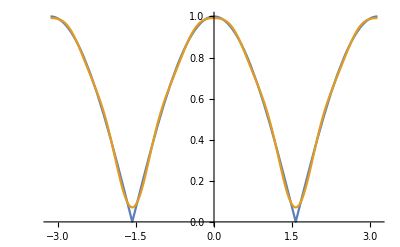

```mathematica
fu[x,8]
Plot[{Abs[Cos[x]],Evaluate@fu[x,8]},{x,-Pi,Pi}]
```

При увелечении порядка разложения, ряд сходится к функции.

##### Пример №12.488

Разложить в ряд Фурье функцию:

f(x)=10-x,  5<x<15, l=5

```mathematica
fu[x_,k_]:=fourier[x,10-x,5,15,k]
```

-(10 Sin[(π x)/5])/π+(5 Sin[(2 π x)/5])/π-(10 Sin[(3 π x)/5])/(3 π)+(5 Sin[(4 π x)/5])/(2 π)-(2 Sin[π x])/π+(5 Sin[(6 π x)/5])/(3 π)-(10 Sin[(7 π x)/5])/(7 π)+(5 Sin[(8 π x)/5])/(4 π)

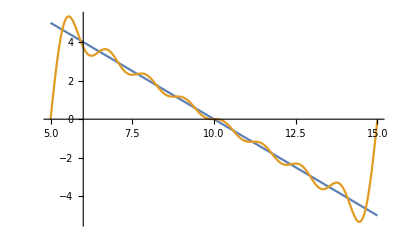

```mathematica
fu[x,8]
Plot[{10-x,Evaluate@fu[x,8]},{x,5,15}]
```

На основе двух тестов будем считать, что написанный модуль проверку прошел.

### 7.3. Ряд Фурье в комплексной форме.

Применим тождества Эйлера для косинуса и синуса ряда (2):

S(t)=a_0/2+∑_(n=1)^∞ (a_n cos(n t)+b_n sin(n t))=a_0/2+∑_(n=1)^∞ (a_n(e^(i n t)+e^(- i n t))/2+b_n(e^(i n t)- e^(-i n t))/(2i))=
=a_0/2+∑_(n=1)^∞ (a_n(e^(i n t)+e^(- i n t))/2-i b_n(e^(i n t)- e^(-i n t))/2)=a_0/2+∑_(n=1)^∞ ((a_n-i b_n)/2 e^(i n t)+(a_n+i b_n)/2 e^(-i n t))

Введем коэффициенты a_n и b_n  отрицательными номерами:

a_-n=a_n
b_-n=b_n

Для которых также справедливы формулы:

a_-n=1/π∫_-π^π f(t)cos(-n t)ⅆt=1/π∫_-π^π f(t)cos(n t)ⅆt=a_n
b_-n=1/π∫_-π^π f(t)sin(-n t)ⅆt=-1/π∫_-π^π f(t)sin(n t )ⅆt=-b_n

Продолжим преобразование:

f(t)=a_0/2+∑_(n=1)^∞ (a_n-i b_n)/2 e^(i n t)+∑_(n=-∞)^-1 (a_n-i b_n)/2 e^(i n t)=∑_(n=-∞)^∞ (a_n-i b_n)/2 e^(i n t)

Обозначим:

c_n=(a_n-i b_n)/2=1/(2π)∫_-π^π f(t)cos(n t)ⅆt-i 1/(2π)∫_-π^π f(t)sin(n t)ⅆt=1/(2π)∫_-π^π f(t)e^(-n t)ⅆt

Итак, в комплексной форме ряд Фурье для функции с произвольным полупериодом l записывается:

f(t)=∑_(n=-∞)^∞ c_n ⅇ^((ⅈ n π x)/l)

c_n=1/(2l)∫_-l^l f(t)ⅇ^(-(ⅈ n π t)/l)ⅆt

##### Пример №12.484

Представить функцию в виде ряда Фурье в комплексной форме:

f(t)=t^2, -π<t<π, l=π

Запишем функцию:

```mathematica
f[t_]:=t^2
```

По формуле (14) запишем коэффициент c_n:

```mathematica
c[n_]:=Integrate[1/(2Pi)f[t] Exp[-I n t],{t,-Pi,Pi}]
```

Запишем функцию ряда Фурье до k-ого порядка:

```mathematica
fu[t_,k_]:=Sum[c[n]Exp[I n t],{n,-k,k}]
```

Получим выражение ряда до 4-ого порядка:

```mathematica
fu[t,4]
```

-2 ⅇ^(-ⅈ t)-2 ⅇ^(ⅈ t)+1/2 ⅇ^(-2 ⅈ t)+1/2 ⅇ^(2 ⅈ t)-2/9 ⅇ^(-3 ⅈ t)-2/9 ⅇ^(3 ⅈ t)+1/8 ⅇ^(-4 ⅈ t)+1/8 ⅇ^(4 ⅈ t)+π^2/3

Сравним, преобразовав данный результат при помощи функции ExpToTrig, с тем, что бы у нас получилось, если бы мы воспользовались модулем fourier:

```mathematica
fourier[t,f[t],-Pi,Pi,4]
fu[t,4]//ExpToTrig
```

π^2/3-4 Cos[t]+Cos[2 t]-4/9 Cos[3 t]+1/4 Cos[4 t]

π^2/3-4 Cos[t]+Cos[2 t]-4/9 Cos[3 t]+1/4 Cos[4 t]

Как и ожидалось, ответы совпадают.

Построим график, чтобы убедится, что ряд сходится к исходной функции:

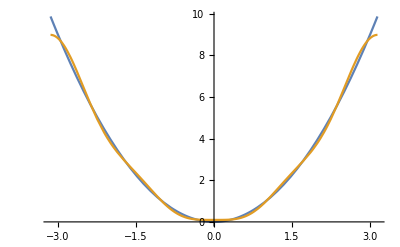

```mathematica
Plot[{f[t],Evaluate@fu[t,4]},{t,-Pi,Pi}]
```

##### Программный модуль

Подобно модулю разложения в тригонометрический ряд, составим модуль разложения в ряд Фурье в комплексной форме:

```mathematica
fourierC[t_,func_,h_,g_,k_]:=Module[{c,l},
l=(g-h)/2;
c[n_]:=1/(2l)Integrate[func Exp[- I Pi/l n t],{t,h,g}];
Sum[c[n]Exp[I Pi/l n t],{n,-k,k}]]
```

##### Пример №12.486

Представить функцию в виде ряда Фурье в комплексной форме:

f(t)=|sin(t)|, -π<t<π, l=π

Выведем результат работы функции fourierC и построим графики исходной функции и полученного ряда:

2/π-(2 ⅇ^(-2 ⅈ t))/(3 π)-(2 ⅇ^(2 ⅈ t))/(3 π)-(2 ⅇ^(-4 ⅈ t))/(15 π)-(2 ⅇ^(4 ⅈ t))/(15 π)

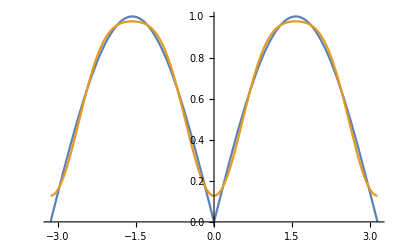

```mathematica
fourierC[t,Abs[Sin[t]],-Pi,Pi,4]
Plot[{Abs[Sin[t]],Evaluate@fourierC[t,Abs[Sin[t]],-Pi,Pi,4]},{t,-Pi,Pi}]
```

Будем считать, что проверка прошла успешно.

### 7.4. Системные функции разложения в ряд Фурье.

Mathematica имеет встроенные функции разложения в ряд Фурье. Рассмотрим на примере:

##### Пример №12.484

Разложить функцию в ряд Фурье периода l:

f(x)=x^2, -π<x<π, l=π

Для решения данной задачи воспользуемся встроенной функцией FourierSeries, имеющей следующую структуру: FourierSeries[expr,t,n] , где expr - выражение или функция, которую требуется разложить в ряд Фурье, t - переменная, по которой ведется разложение, n- высший порядок разложения.

Запишем исходную функцию:

```mathematica
f[x_]:=x^2
```

Теперь получим разложение в ряд до 6ого члена.

```mathematica
FourierSeries[x^2,x,6]
```

-2 ⅇ^(-ⅈ x)-2 ⅇ^(ⅈ x)+1/2 ⅇ^(-2 ⅈ x)+1/2 ⅇ^(2 ⅈ x)-2/9 ⅇ^(-3 ⅈ x)-2/9 ⅇ^(3 ⅈ x)+1/8 ⅇ^(-4 ⅈ x)+1/8 ⅇ^(4 ⅈ x)-2/25 ⅇ^(-5 ⅈ x)-2/25 ⅇ^(5 ⅈ x)+1/18 ⅇ^(-6 ⅈ x)+1/18 ⅇ^(6 ⅈ x)+π^2/3

Как мы видим, по умолчанию, Mathematica раскладывает в ряд в комплексной форме, можем перейти в более привычной для нас, тригонометрической форме:

```mathematica
FourierSeries[x^2,x,6]//ExpToTrig
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]

Как мы видим, функция четная, функции синуса в разложении отсутствуют.

Найдем формулу n-ого коэффициента при помощи функции FourierCoefficient:

```mathematica
FourierCoefficient[x^2,x,n]
```

(2 (-1)^n)/n^2

Напоминаем, что это коэффициент в разложении в комплексной форме с_n, он не равен коэффициентам a_n или b_n.

Также находим свободный коэффициент:

```mathematica
FourierCoefficient[x^2,x,0]
```

π^2/3

Составим функцию ряда:

```mathematica
fu[x_,n_]:=FourierSeries[t^2,t,n]/.t-> x
```

```mathematica
fu[x,6]//ExpToTrig
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]

Покажем график  исходной функции и ряда Фурье до 5ого порядка:

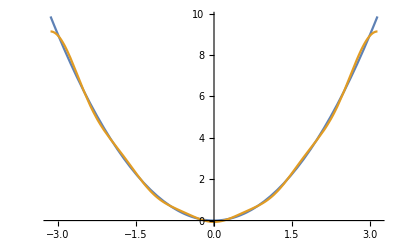

```mathematica
Plot[{f[x],Evaluate@fu[x,5]},{x,-Pi,Pi}]
```

##### Пример №12.496

Доопределяя необходимым образом заданную в промежутке функцию до переодической, получить для нее: а) ряд Фурье по косинусам б) ряд Фурье по синусам.

f(x)=x sin(x), 0<x<π

Так как данная функция четная, получим выражение ряда в общей форме.

Для этого запишем и посмотрим заданную функцию:

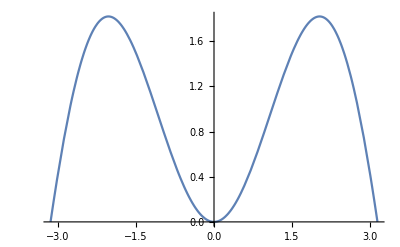

```mathematica
f[x_]:=x Sin[x]
Plot[f[x],{x,-Pi,Pi}]
```

Так как данная функция четная, в разложении будут отсутствовать члены с синусом, тогда:

c_n=(a_n-i b_n)/2=(a_n-i 0)/2⇒a_n=2 c_n

Получим выражение для нулевого и n-ого коэффициента:

```mathematica
FourierCoefficient[f[x],x,n]
```

(-1)^(1+n)/(-1+n^2)

Отсюда следует, что

a_n=(2(-1)^(n+1))/(n^2-1)

Найдем значение коэффициента при n=1:

```mathematica
FourierCoefficient[f[x],x,1]
```

-1/4

Тогда ряд запишем в виде:

f(x)=1-1/2 cos(x)+∑_(n=2)^∞ (2(-1)^(n+1))/(n^2-1)cos(n x)

Ряд Фурье для исходной функции получим при помощи встроенной опции FourierSinSeries (аналогично существует опция FourierCosSeries),  она имеет ту же структуру, что и FourierSeries:

```mathematica
FourierSinSeries[f[x],x,8]
```

1/2 π Sin[x]-(16 Sin[2 x])/(9 π)-(32 Sin[4 x])/(225 π)-(48 Sin[6 x])/(1225 π)-(64 Sin[8 x])/(3969 π)

Изобразим график функции и ряда:

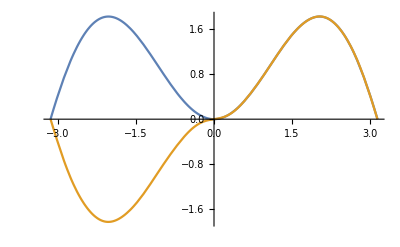

```mathematica
Plot[{f[x],Evaluate@FourierSinSeries[f[x],x,8]},{x,-Pi,Pi}]
```

Как видно из графика, исходная функция была доопределена до несимметричной функции, у которой отстуствует косинус в разложении в ряд.

Коэффициент b_n получим при помощи функции FourierSinCoefficient:

```mathematica
FourierSinCoefficient[f[x],x,n]
```

-(4 (1+(-1)^n) n)/((-1+n^2)^2 π)

```mathematica
FourierSinCoefficient[f[x],x,1]
```

π/2

Тогда ряд запишется в виде:

f(x)=π/2 sin(x)-4/π∑_(n=2)^∞ ((1+(-1)^n) n)/((-1+n^2)^2)sin(n x)